```mathematica
1+Sum[(-1)^k Log[1+k]/k,{k,1,Infinity}]//N
```

0.607741

```mathematica
NIntegrate[(1/(2r))*(PolyGamma[0, (r + 1)/2]-PolyGamma[0, r/2]), {r, 1, Infinity}]
```

0.607741

```mathematica
Series[(1/(2r))*(PolyGamma[0, (r + 1)/2]-PolyGamma[0, r/2]),{r,Infinity,20}]
```

1/(2 r^2)+1/(4 r^3)-1/(8 r^5)+1/(4 r^7)-17/(16 r^9)+31/(4 r^11)-691/(8 r^13)+5461/(4 r^15)-929569/(32 r^17)+3202291/(4 r^19)+O[1/r]^21

```mathematica
Integrate[1/(y^z+1),z]
```

z-Log[1+y^z]/Log[y]

```mathematica
NIntegrate[x^y^z, {x, 0, 1}, {y, 0, 1}, {z, 0, 1}]
NIntegrate[Log[y,2y] - Log[y,y + 1], {y, 0, 1}]
NIntegrate[(-PolyGamma[0, r/2] + PolyGamma[0, (1 + r)/2])/(2*r), {r, 1, Infinity}]
1+NSum[(-1)^k Log[1+k]/k,{k,1,Infinity}]
```

0.607741

0.607741

0.607741

«1 more identical outputs»

```mathematica
Function[n,Integrate[Power@@Array[Subscript[x,#]&,n],##]&@@Array[{Subscript[x,#],0,1}&,n]]@4
```

∫_0^1 ∫_0^1 If[x_3^x_4>1,1/2 (2 π Csc[π x_3^-x_4]-HarmonicNumber[-1/2 x_3^-x_4]+HarmonicNumber[-1/2-x_3^-x_4/2]) x_3^-x_4,Integrate[Gamma[x_3^-x_4] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4-Gamma[x_3^-x_4,-Log[x_1]] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4,{x_1,0,1},Assumptions→Re[x_3^-x_4]≥1]]ⅆ x_4ⅆ x_3

```mathematica
Function[n,Integrate[Power@@Array[Subscript[x,#]&,n],##]&@@Reverse[Array[{Subscript[x,#],0,1}&,n]]]@4
```

∫_0^1 -(2 1/2 (1+1/x_3)-2 1/(2 x_3)+log(π))/(2 log(x_3))ⅆ x_3

```mathematica
Function[n,Integrate[Power@@Array[Subscript[x,#]&,n],##]&@@Reverse[Array[{Subscript[x,#],0,1}&,n]]]@2
```

Log[2]

```mathematica
Function[n,Integrate[Power@@Array[Subscript[x,#]&,n],##]&@@Reverse[Array[{Subscript[x,#],0,1}&,n]]]@3
```

∫_0^1 (PolyGamma[0,1/2 (1+1/x_3)]-PolyGamma[0,1/(2 x_3)])/(2 x_3)ⅆ x_3

```mathematica
Function[n,Integrate[Power@@Array[Subscript[x,#]&,n],##]&@@Reverse[Array[{Subscript[x,#],0,1}&,n]]]@5
```

```mathematica
Integrate[x^y^z, {x, 0, 1}, {y, 0, 1}, {z, 0, 1}]
Integrate[Log[y,2*y] - Log[y,y + 1], {y, 0, 1}]
Integrate[(-PolyGamma[0, r/2] + PolyGamma[0, (1 + r)/2])/(2*r), {r, 1, Infinity}]
1+Sum[(-1)^k Log[1+k]/k,{k,1,Infinity}]
```

```mathematica
Integrate[(-PolyGamma[0, r/2] + PolyGamma[0, (1 + r)/2])/(2*r), {r, 1, Infinity}]
```

```mathematica
1+Sum[(-1)^k Log[1+k]/k,{k,1,Infinity}]
```

```mathematica
Integrate[Power@@Array[Subscript[x,#]&,4],##]&@@@Permutations[Array[{Subscript[x,#],0,1}&,4]]
```

{∫_0^1 ∫_0^1 If[x_3^x_4>1,1/2 (2 π Csc[π x_3^-x_4]-HarmonicNumber[-1/2 x_3^-x_4]+HarmonicNumber[-1/2-x_3^-x_4/2]) x_3^-x_4,Integrate[Gamma[x_3^-x_4] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4-Gamma[x_3^-x_4,-Log[x_1]] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4,{x_1,0,1},Assumptions→Re[x_3^-x_4]≥1]]ⅆ x_4ⅆ x_3,∫_0^1 ∫_0^1 If[x_3^x_4>1,1/2 (2 π Csc[π x_3^-x_4]-HarmonicNumber[-1/2 x_3^-x_4]+HarmonicNumber[-1/2-x_3^-x_4/2]) x_3^-x_4,Integrate[Gamma[x_3^-x_4] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4-Gamma[x_3^-x_4,-Log[x_1]] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4,{x_1,0,1},Assumptions→Re[x_3^-x_4]≥1]]ⅆ x_3ⅆ x_4,∫_0^1 ∫_0^1 If[x_3^x_4>1,1/2 (2 π Csc[π x_3^-x_4]-HarmonicNumber[-1/2 x_3^-x_4]+HarmonicNumber[-1/2-x_3^-x_4/2]) x_3^-x_4,Integrate[Gamma[x_3^-x_4] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4-Gamma[x_3^-x_4,-Log[x_1]] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4,{x_1,0,1},Assumptions→Re[x_3^-x_4]≥1]]ⅆ x_4ⅆ x_3,∫_0^1 ∫_0^1 If[x_3^x_4>1,1/2 (2 π Csc[π x_3^-x_4]-HarmonicNumber[-1/2 x_3^-x_4]+HarmonicNumber[-1/2-x_3^-x_4/2]) x_3^-x_4,Integrate[Gamma[x_3^-x_4] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4-Gamma[x_3^-x_4,-Log[x_1]] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4,{x_1,0,1},Assumptions→Re[x_3^-x_4]≥1]]ⅆ x_4ⅆ x_3,∫_0^1 ∫_0^1 If[x_3^x_4>1,1/2 (2 π Csc[π x_3^-x_4]-HarmonicNumber[-1/2 x_3^-x_4]+HarmonicNumber[-1/2-x_3^-x_4/2]) x_3^-x_4,Integrate[Gamma[x_3^-x_4] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4-Gamma[x_3^-x_4,-Log[x_1]] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4,{x_1,0,1},Assumptions→Re[x_3^-x_4]≥1]]ⅆ x_3ⅆ x_4,∫_0^1 ∫_0^1 If[x_3^x_4>1,1/2 (2 π Csc[π x_3^-x_4]-HarmonicNumber[-1/2 x_3^-x_4]+HarmonicNumber[-1/2-x_3^-x_4/2]) x_3^-x_4,Integrate[Gamma[x_3^-x_4] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4-Gamma[x_3^-x_4,-Log[x_1]] (-Log[x_1])^(-x_3^-x_4) x_3^-x_4,{x_1,0,1},Assumptions→Re[x_3^-x_4]≥1]]ⅆ x_3ⅆ x_4,∫_0^1 ∫_0^1 If[Re[(-1)^(x_3^-x_4)]≥1||Re[(-1)^(x_3^-x_4)]≤0||(-1)^(x_3^-x_4)∉Reals,1/2 (-PolyGamma[0,x_3^-x_4/2]+PolyGamma[0,1/2 (1+x_3^-x_4)]) x_3^-x_4,Integrate[1/(1+x_2^(x_3^x_4)),{x_2,0,1},Assumptions→((-1)^(x_3^-x_4)∈Reals&&0<(-1)^(x_3^-x_4)<1&&0<Re[(-1)^(x_3^-x_4)]<1)||Re[x_3^x_4]≤0]]ⅆ x_4ⅆ x_3,∫_0^1 ∫_0^1 If[Re[(-1)^(x_3^-x_4)]≥1||Re[(-1)^(x_3^-x_4)]≤0||(-1)^(x_3^-x_4)∉Reals,1/2 (-PolyGamma[0,x_3^-x_4/2]+PolyGamma[0,1/2 (1+x_3^-x_4)]) x_3^-x_4,Integrate[1/(1+x_2^(x_3^x_4)),{x_2,0,1},Assumptions→((-1)^(x_3^-x_4)∈Reals&&0<(-1)^(x_3^-x_4)<1&&0<Re[(-1)^(x_3^-x_4)]<1)||Re[x_3^x_4]≤0]]ⅆ x_3ⅆ x_4,∫_0^1 ∫_0^1 If[Re[(-1)^(x_3^-x_4)]≥1||Re[(-1)^(x_3^-x_4)]≤0||(-1)^(x_3^-x_4)∉Reals,1/2 (-PolyGamma[0,x_3^-x_4/2]+PolyGamma[0,1/2 (1+x_3^-x_4)]) x_3^-x_4,Integrate[1/(1+x_2^(x_3^x_4)),{x_2,0,1},Assumptions→((-1)^(x_3^-x_4)∈Reals&&0<(-1)^(x_3^-x_4)<1&&0<Re[(-1)^(x_3^-x_4)]<1)||Re[x_3^x_4]≤0]]ⅆ x_4ⅆ x_3,∫_0^1 ∫_0^1 If[Re[(-1)^(x_3^-x_4)]≥1||Re[(-1)^(x_3^-x_4)]≤0||(-1)^(x_3^-x_4)∉Reals,1/2 (-PolyGamma[0,x_3^-x_4/2]+PolyGamma[0,1/2 (1+x_3^-x_4)]) x_3^-x_4,Integrate[1/(1+x_2^(x_3^x_4)),{x_2,0,1},Assumptions→((-1)^(x_3^-x_4)∈Reals&&0<(-1)^(x_3^-x_4)<1&&0<Re[(-1)^(x_3^-x_4)]<1)||Re[x_3^x_4]≤0]]ⅆ x_4ⅆ x_3,∫_0^1 ∫_0^1 If[Re[(-1)^(x_3^-x_4)]≥1||Re[(-1)^(x_3^-x_4)]≤0||(-1)^(x_3^-x_4)∉Reals,1/2 (-PolyGamma[0,x_3^-x_4/2]+PolyGamma[0,1/2 (1+x_3^-x_4)]) x_3^-x_4,Integrate[1/(1+x_2^(x_3^x_4)),{x_2,0,1},Assumptions→((-1)^(x_3^-x_4)∈Reals&&0<(-1)^(x_3^-x_4)<1&&0<Re[(-1)^(x_3^-x_4)]<1)||Re[x_3^x_4]≤0]]ⅆ x_3ⅆ x_4,∫_0^1 ∫_0^1 If[Re[(-1)^(x_3^-x_4)]≥1||Re[(-1)^(x_3^-x_4)]≤0||(-1)^(x_3^-x_4)∉Reals,1/2 (-PolyGamma[0,x_3^-x_4/2]+PolyGamma[0,1/2 (1+x_3^-x_4)]) x_3^-x_4,Integrate[1/(1+x_2^(x_3^x_4)),{x_2,0,1},Assumptions→((-1)^(x_3^-x_4)∈Reals&&0<(-1)^(x_3^-x_4)<1&&0<Re[(-1)^(x_3^-x_4)]<1)||Re[x_3^x_4]≤0]]ⅆ x_3ⅆ x_4,1/2 ∫_0^1 -(Log[π]-2 Log[Cos[π/(2 x_3)]]+2 Log[Sin[π/(2 x_3)]]-2 LogGamma[1/2-1/(2 x_3)]+2 LogGamma[1-1/(2 x_3)])/Log[x_3]ⅆ x_3,1/2 ∫_0^1 -(Log[π]-2 Log[Cos[π/(2 x_3)]]+2 Log[Sin[π/(2 x_3)]]-2 LogGamma[1/2-1/(2 x_3)]+2 LogGamma[1-1/(2 x_3)])/Log[x_3]ⅆ x_3,1/2 ∫_0^1 -(2 Log[Gamma[1/2 (1+1/x_3)]]+Log[π/Gamma[1/(2 x_3)]^2])/Log[x_3]ⅆ x_3,1/2 ∫_0^1 -(2 Log[Gamma[1/2 (1+1/x_3)]]+Log[π/Gamma[1/(2 x_3)]^2])/Log[x_3]ⅆ x_3,∫_0^1 -(Log[π]-2 Log[Cos[π/(2 x_3)]]+2 Log[Sin[π/(2 x_3)]]-2 LogGamma[1/2-1/(2 x_3)]+2 LogGamma[1-1/(2 x_3)])/(2 Log[x_3])ⅆ x_3,∫_0^1 -(2 Log[Gamma[1/2 (1+1/x_3)]]+Log[π/Gamma[1/(2 x_3)]^2])/(2 Log[x_3])ⅆ x_3,∫_0^1 If[Re[Log[x_3]]>0,-(Log[π]+2 Log[Tan[π/(2 x_3)]]-2 LogGamma[1/2-1/(2 x_3)]+2 LogGamma[1-1/(2 x_3)])/(2 Log[x_3]),Integrate[π Csc[π x_3^-x_4] x_3^-x_4-1/2 HarmonicNumber[-1/2 x_3^-x_4] x_3^-x_4+1/2 HarmonicNumber[-1/2-x_3^-x_4/2] x_3^-x_4,{x_4,0,1},Assumptions→Re[Log[x_3]]≤0]]ⅆ x_3,∫_0^1 If[Re[Log[x_3]]>0,-(Log[π]+2 Log[Tan[π/(2 x_3)]]-2 LogGamma[1/2-1/(2 x_3)]+2 LogGamma[1-1/(2 x_3)])/(2 Log[x_3]),Integrate[π Csc[π x_3^-x_4] x_3^-x_4-1/2 HarmonicNumber[-1/2 x_3^-x_4] x_3^-x_4+1/2 HarmonicNumber[-1/2-x_3^-x_4/2] x_3^-x_4,{x_4,0,1},Assumptions→Re[Log[x_3]]≤0]]ⅆ x_3,∫_0^1 -(Log[π]+2 LogGamma[1/2 (1+1/x_3)]-2 LogGamma[1/(2 x_3)])/(2 Log[x_3])ⅆ x_3,∫_0^1 -(Log[π]+2 LogGamma[1/2 (1+1/x_3)]-2 LogGamma[1/(2 x_3)])/(2 Log[x_3])ⅆ x_3,∫_0^1 If[Re[Log[x_3]]>0,-(Log[π]+2 Log[Tan[π/(2 x_3)]]-2 LogGamma[1/2-1/(2 x_3)]+2 LogGamma[1-1/(2 x_3)])/(2 Log[x_3]),Integrate[π Csc[π x_3^-x_4] x_3^-x_4-1/2 HarmonicNumber[-1/2 x_3^-x_4] x_3^-x_4+1/2 HarmonicNumber[-1/2-x_3^-x_4/2] x_3^-x_4,{x_4,0,1},Assumptions→Re[Log[x_3]]≤0]]ⅆ x_3,∫_0^1 -(Log[π]+2 LogGamma[1/2 (1+1/x_3)]-2 LogGamma[1/(2 x_3)])/(2 Log[x_3])ⅆ x_3}

```mathematica
Integrate[Gamma[1+1/Subscript[x, 3]] (-Log[Subscript[x, 1]])^(-1/Subscript[x, 3])-(Gamma[1/Subscript[x, 3],-Log[Subscript[x, 1]]] (-Log[Subscript[x, 1]])^(-1/Subscript[x, 3]))/Subscript[x, 3],{Subscript[x, 1],0,1},{Subscript[x, 3],0,1}]
```

```mathematica
,
```

```mathematica
Gamma[1+1/Subscript[x, 3]] (-Log[Subscript[x, 1]])^(-1/Subscript[x, 3])-(Gamma[1/Subscript[x, 3],-Log[Subscript[x, 1]]] (-Log[Subscript[x, 1]])^(-1/Subscript[x, 3]))/Subscript[x, 3]/.{Subscript[x, 1]->p,Subscript[x, 3]->q}
```

Gamma[1+1/q] (-Log[p])^(-1/q)-(Gamma[1/q,-Log[p]] (-Log[p])^(-1/q))/q

```mathematica
NIntegrate[E^r(r-Log[E^r+1]+Log[2])/r,{r,-Infinity,0}]
```

0.607741

```mathematica
Sinh[x]Sin[x]
```

Sin[x] Sinh[x]

```mathematica
∫Sin[x] Sinh[x]SinIntegral[x]SinhIntegral[x]ⅆx
```

∫Sin[x] Sinh[x] SinhIntegral[x] SinIntegral[x]ⅆx

```mathematica
CosIntegral[]
```

```mathematica
Sin[x]ArcSin[x]
```

ArcSin[x] Sin[x]

```mathematica
∫ArcSin[x] Sin[x]ⅆx
```

∫ArcSin[x] Sin[x]ⅆx

```mathematica
DSolveValue[{f'[x]==g[x],g'[x]==f[x]},{f[x],g[x]},x]
DSolveValue[{f'[x]==-g[x],g'[x]==f[x],f[0]==0},{f[x],g[x]},x]
DSolveValue[{f'[x]==-g[x],g'[x]==-f[x]},{f[x],g[x]},x]
```

{1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2],1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]}

{-C[2] Sin[x],C[2] Cos[x]}

{1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2],-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]}

```mathematica
DSolveValue[{f'[x]==g[x],g'[x]==h[x],h'[x]==f[x]},{f[x],g[x],h[x]},x]
```

{1/3 ⅇ^(-x/2) C[1] (ⅇ^(3 x/2)+2 Cos[(√3 x)/2])+1/3 ⅇ^(-x/2) C[3] (ⅇ^(3 x/2)-Cos[(√3 x)/2]-√3 Sin[(√3 x)/2])+1/3 ⅇ^(-x/2) C[2] (ⅇ^(3 x/2)-Cos[(√3 x)/2]+√3 Sin[(√3 x)/2]),1/3 ⅇ^(-x/2) C[2] (ⅇ^(3 x/2)+2 Cos[(√3 x)/2])+1/3 ⅇ^(-x/2) C[1] (ⅇ^(3 x/2)-Cos[(√3 x)/2]-√3 Sin[(√3 x)/2])+1/3 ⅇ^(-x/2) C[3] (ⅇ^(3 x/2)-Cos[(√3 x)/2]+√3 Sin[(√3 x)/2]),1/3 ⅇ^(-x/2) C[3] (ⅇ^(3 x/2)+2 Cos[(√3 x)/2])+1/3 ⅇ^(-x/2) C[2] (ⅇ^(3 x/2)-Cos[(√3 x)/2]-√3 Sin[(√3 x)/2])+1/3 ⅇ^(-x/2) C[1] (ⅇ^(3 x/2)-Cos[(√3 x)/2]+√3 Sin[(√3 x)/2])}

```mathematica
DSolveValue[{f'[x]==f[x]},f[x],x]
DSolveValue[{f'[x]==-f[x]},f[x],x]
```

ⅇ^x C[1]

ⅇ^-x C[1]

```mathematica
Quit
```

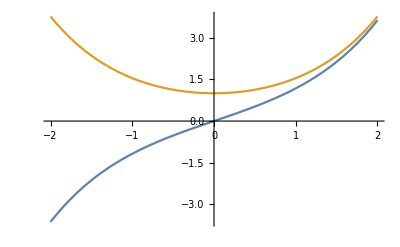

{(d x+(2 (b c-a d) ArcTan[(b-a Tanh[x/2])/(√(-a^2-b^2))])/(√(-a^2-b^2)))/b,(d x+(2 (-b c+a d) ArcTan[((a-b) Tanh[x/2])/(√(-a^2+b^2))])/(√(-a^2+b^2)))/b,((a c-b d) x+(-b c+a d) Log[a Cosh[x]+b Sinh[x]])/((a-b) (a+b)),((a c-b d) x+(-b c+a d) Log[b Cosh[x]+a Sinh[x]])/((a-b) (a+b)),(c x+(2 (b c-a d) ArcTan[((-a+b) Tanh[x/2])/(√((a-b) (a+b)))])/(√((a-b) (a+b))))/a,(c x+(2 (-b c+a d) ArcTan[(a-b Tanh[x/2])/(√(-a^2-b^2))])/(√(-a^2-b^2)))/a}

```mathematica
Plot[{Sinh[x],Cosh[x]},{x,-2,2}]
```